```mathematica
M=2000;
P=1000;
pq0=1000;
pL=1;
b=3/100;
h=65/1000;
pE=210*10^9;
eps=10^-10;
```

```mathematica
prm={M0->M,M1->M,P2->P,q0->pq0,L->pL,b->pb,h->ph,EE->pE,J3->(b*h^3)/12};
eps=10^-10;

MyPlot[f_,a_,b_,arg_,y_]:=Plot[f, {x,a,b},AxesLabel->{Style[arg,Black,16, FontFamily->"Times"],Style[y,Black,16, FontFamily->"Times"]},LabelStyle->Directive[Black,14, FontFamily->"Times"],PlotStyle->{Black,Thickness[0.004]},ImageSize->500,PlotRange->All];
MyPlotEpur[f_,a_,b_,arg_,y_,n_]:=
Show[MyPlot[f,a,b,arg,y],Graphics[{Darker@Black,Thickness[0.003],Line[{{1+eps,0.0},{1+eps,f/.{x->1+eps}}}],Line[{{2+eps,0.0},{2+eps,f/.{x->2+eps}}}]}~Join~Table[Line[{{a+(b-a)/(3n)*i,0.0},{a+(b-a)/(3n)*i,f/.{x->a+(b-a)/(3n)*i}}}],{i,1,3n}]~Join~{Opacity[1]}],MyPlot[f,a,b,arg,y]];
```

```mathematica
Задание 3
```

3 Задание

```mathematica
sol3=Solve[{R3+P1+P2+P0-q0*2L==0,M0-M1+L*P1+2L*P2+3L R3-q0*2L*L==0},{P0,P1}]⟦1⟧//Simplify;
Print["P1 = ",P1/.sol3];
Print["P0 = ",P0/.sol3];
```

P1 = (-M0+M1+L (-2 P2+2 L q0-3 R3))/L

P0 = (M0-M1+L P2+2 L R3)/L

```mathematica
Задание 4
```

4 Задание

P0 = 2 R3

P1 = -3 R3

M3(x1) = P0 (Piecewise[{{ξ, ξ>0}, {0, True}}])+R3 (Piecewise[{{-3 L+ξ, -3 L+ξ>0}, {0, True}}])+P1 (Piecewise[{{-L+ξ, -L+ξ>0}, {0, True}}])

Q3(x1) = P0 f0[x1]+R3 f0[-3 L+x1]+P1 f0[-L+x1]

M3(x1) = R3 (2 (Piecewise[{{ξ, ξ>0}, {0, True}}])+(Piecewise[{{-3 L+ξ, ξ>3 L}, {0, True}}])-3 (Piecewise[{{-L+ξ, ξ>L}, {0, True}}]))

Q3(x1) = R3 (2 f0[x1]+f0[-3 L+x1]-3 f0[-L+x1])

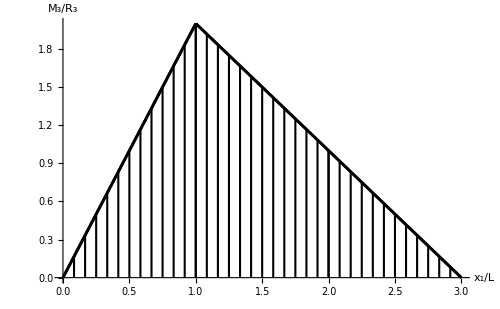

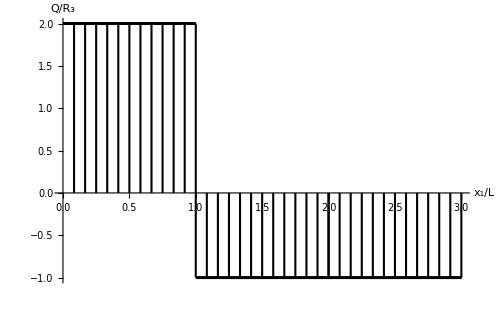

```mathematica
f[n_,ξ_]:=Piecewise[{{ξ^n/(n!), ξ>0}, {0, ξ≤0}}];
sol41=Solve[{R3+P1+P0==0,L*P1+3L R3==0},{P0,P1}]⟦1⟧//Simplify;
Print["P0 = ",P0/.sol41];
Print["P1 = ",P1/.sol41];
M31[ξ_]:=P0 *f[1, ξ]+ R3*f[1,ξ-3L]+P1*f[1,ξ-L]/.sol41//Simplify;
Q31[ξ_]:=M31'[ξ]//Simplify;
Print["M3(x1) = ",  P0 *f[1, ξ]+R3*f[1,ξ-3L]+P1*f[1,ξ-L] ];
Print["Q3(x1) = ",P0*f0[x1]+ R3*f0[x1-3L]+P1*f0[x1-L]];
Print["M3(x1) = ",P0 *f[1, ξ]+ R3*f[1,ξ-3L]+P1*f[1,ξ-L] /.sol41//Simplify];
Print["Q3(x1) = ",P0*f0[x1]+ R3*f0[x1-3L]+P1*f0[x1-L]/.sol41//Simplify];
Print@MyPlotEpur[(M31[x]/.{R3->1}/.prm),0,3,"x_1/L","M_3/R_3",12];
Print@MyPlotEpur[(Q31[x]/.{R3->1}/.prm),0,3,"x_1/L","Q/R_3",12];
```

```mathematica
Задание 5
```

5 Задание

```mathematica
f[x_,n_]:=Piecewise[{{0, x≤0}, {x^n/(n!), x>0}}]
```

```mathematica
w5[x_]:=w50+w550 x + 1/(EE J) (2 R3 *f[x, 3] - 3 R3  f[x-L,3](*+R3 f[x-3L,3]*));
```

```mathematica
tempW5=Assuming[L>0,Simplify@Solve[{w5[L]==0,w5[0]==0},{w50,w550}]]
WW5[x_]:=w5[x]/.w50->tempW5[[1, 1, 2]]/.w550->tempW5[[1, 2, 2]];
Assuming[L>0,WW5[x1]];
Assuming[L>0,WW5[3L]]/.L->1
```

{{w50→0,w550→-(L^2 R3)/(3 EE J)}}

(4 R3)/(EE J)

```mathematica
6 графики;
```

```mathematica
sol61=Solve[{P1+P2+P0-q0*2L==0,M0-M1+L*P1+2L*P2-2 L^2*q0==0},{P0,P1}]⟦1⟧//Simplify;
Print["P1 = ",P1/.sol61];
Print["P0 = ",P0/.sol61];
```

P1 = (-M0+M1+2 L (-P2+L q0))/L

P0 = (M0-M1+L P2)/L

```mathematica
Print["К пункту 6"]
Print["P1 = ",P1/.sol61/.prm]
Print["P0 = ",P0/.sol61/.prm]
```

К пункту 6

P1 = 0

P0 = 1000

```mathematica
MM[ξ_]:=M1*f[ξ-L, 0]-M0*f[ξ, 0]+P1*f[ξ-L, 1]+P2*f[ξ-2L, 1]-q0*f[ξ, 2]+q0*f[ξ-2L, 2]/.sol61//Simplify;
QQ[ξ_]:=M32'[ξ]//Simplify;
Show[Plot[Piecewise[{{QQ,0<x< 1},{QQ,1<x< 2},{QQ,2<x< 3}}],{x,0,3}, AxesLabel->{Style["x_1",Black,16, FontFamily->"Times"],Style["Q(x_1)",Black,16, FontFamily->"Times"]},LabelStyle->Directive[Black,15, FontFamily->"Times"],PlotStyle->{Black,Thickness[0.004]},ImageSize->500,PlotRange->All],Graphics[{Darker@Black,Table[Line[{{x,0},{x,QQ}}],{x,0.01,0.99,0.1}]}],Graphics[{Darker@Black,Table[Line[{{x,0},{x,QQ}}],{x,1.01,1.99,0.1}]}],Graphics[{Darker@Black,Table[Line[{{x,0},{x,QQ}}],{x,2.01,2.99,0.1}]}]]
```

SetDelayed::write: Tag Plus in … is Protected.

-Graphics-

```mathematica
Задание 7;
```

```mathematica
f[x_,n_]:=Piecewise[{{0, x≤0}, {x^n/(n!), x>0}}]
```

```mathematica
w7[x_]:=w70 + w770 x + 1/(EE J)(P0 f[x, 3]+P1 f[x-L,3] -M0  f[x,2]+M1  f[x-L,2]+ P2 f[x-2L,3]-q0*f[x, 4]+q0 f[x-2L,4] )/.sol61
```

```mathematica
w7Vals= Assuming[L>0, Simplify@Solve[{w7[L]==0,w7[0]==0},{w70,w770}]]
WW7[x_]:=w7[x] /.w70->w7Vals[[1, 1,2]]/.w770->w7Vals[[1, 2, 2]];
```

{{w70→0,w770→(L (8 M0+4 M1+L (-4 P2+L q0)))/(24 EE J)}}

```mathematica
WW7[3L]/.L->1
```

(8 M0+4 M1-4 P2+q0)/(8 EE J)+(-(9 M0)/2+2 M1+P2/6+9/2 (M0-M1+P2)-(10 q0)/3+4/3 (-M0+M1+2 (-P2+q0)))/(EE J)

```mathematica
Задание 8;
```

```mathematica
RSOULUTION=Assuming[L>0,Solve[WW7[3L]+WW5[3L]==0,R3]][[1, 1, 2]]
R3res=RSOULUTION/.q->pq0/.prm;
Print["R3 = ",R3res//N]
```

(8 L^2 M0+16 L^2 M1-36 L^3 P2+13 L^4 q0)/(96 L^3)

R3 = 260.417

```mathematica
Print["К пункту 3"]
Print["P1 = ",(-M0+M1+L (-2 P2+2 L q0-3 R3))/L/.prm/.R3->R3res]
Print["P0 = ", (M0-M1+L P2+2 L R3)/L/.prm/.R3->R3res]
```

К пункту 3

P1 = 1/32 (121000-32 P1)

P0 = 1000+1/48 (-121000+32 P1)

```mathematica
(-M0+M1+L (-2 P2+2 L q0-3 R3))/L/.R3->R3res
(M0-M1+L P2+2 L R3)/L/.R3->R3res
```

(-M0+M1+L (1/32 (121000-32 P1)-2 P2+2 L q0))/L

(M0-M1+1/48 L (-121000+32 P1)+L P2)/L

```mathematica
f1[L]
```

f1[L]

```mathematica
Задание 9
```

9 Задание

```mathematica
MMM=Assuming[3>x> 0, R3*f[x, 1]-3R3*f[x-L, 1]+MM/.R3->R3res /.P1->0/.P2->P/.M1->M/.M0->M/.L->pL];
Show[Plot[MMM,{x,0,3}, AxesLabel->{Style["x_1",Black,20, FontFamily->"Times"],Style["M(x_1)",Black,20, FontFamily->"Times"]},LabelStyle->Directive[Black,15, FontFamily->"Times"],PlotStyle->{Black,Thickness[0.004]},ImageSize->500,PlotRange->{{0,3},{0,30000}}],Graphics[{Darker@Black,Table[Line[{{x,0},{x,MMM}}],{x,0,3,0.1}]}]]
```

-Graphics-

```mathematica
QQQ=MMM';
Show[Plot[Piecewise[{{QQQ,0<x< 1},{QQQ,1<x< 2},{QQQ,2<x< 3}}],{x,0,3}, AxesLabel->{Style["x_1",Black,16, FontFamily->"Times"],Style["Q(x_1)",Black,16, FontFamily->"Times"]},LabelStyle->Directive[Black,15, FontFamily->"Times"],PlotStyle->{Black,Thickness[0.004]},ImageSize->500,PlotRange->All],Graphics[{Darker@Black,Table[Line[{{x,0},{x,QQQ}}],{x,0.01,0.99,0.1}]}],Graphics[{Darker@Black,Table[Line[{{x,0},{x,QQQ}}],{x,1.01,1.99,0.1}]}],Graphics[{Darker@Black,Table[Line[{{x,0},{x,QQQ}}],{x,2.01,2.99,0.1}]}]]
```

-Graphics-

```mathematica
f[x_,n_]:=Piecewise[{{0, x≤0}, {x^n/(n!), x>0}}]
```

```mathematica
w[x_]:=WRW0  /.{M1->M, M0->M, M->2000,P2->1000,q->1000,L->1,R3->R3res,P1->0,J->(0.65^3 0.03)/12,EE->210 10^9} (*w[x] := w5[x] + w7[x]*)
```

```mathematica
Simplify@w[x]
```

WRW0

```mathematica
Plot[w[x],{x,0,3},AxesLabel->{Style["x_1",Black,20, FontFamily->"Times"],Style["w(x_1)",Black,20, FontFamily->"Times"]},LabelStyle->Directive[Black,15, FontFamily->"Times"],PlotStyle->{Black,Thickness[0.003]},ImageSize->500,PlotRange->All]
```

-Graphics-

```mathematica
Задание 10;
FindMaxValue[- pq0 x^2/2+0(x-pL)-M+pq0*(x-pL)^2-P(x-2pL)+R3res x,{x,1,0,3}]
Mmax=M;
W3=(b*h^2)/6;
σmax=Mmax/W3;
Print["σmax = ", N[σmax*10^-6/.prm]," МПа"];
```

FindMaxValue::nrnum: The function value 1500.-0.0104167 (-121000+32 P1) is not a real number at {x} = {1.}.

FindMaxValue[1/2 (-pq0) x^2+0 (x-pL)-M+pq0 (x-pL)^2-P (x-2 pL)+R3res x,{x,1,0,3}]

σmax = 94.6746 МПа